```mathematica
(*get association of resources,name of local host and remove local host from available resources*)
(*hosts=Counts[ReadList[Environment["NODEFILE"],"String"]]
local=First[StringSplit[Environment["HOSTNAME"],"."]]
hosts[local]--;
(*launch subkernels and connect them to the controlling Wolfram Kernel*)
Needs["SubKernels`RemoteKernels`"];
Map[If[hosts[#]>0,LaunchKernels[RemoteMachine[#,"ssh -x -f -l `3` `1` /gpfs/runtime/opt/mathematica/12.0/Executables/wolfram -wstp -linkmode Connect `4` -linkname '`2`' -subkernel -noinit",hosts[#]]]]&,Keys[hosts]];
dir=DirectoryName[$InputFileName];*)
```

```mathematica
Unprotect[Out];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
<<NDSolve`FEM`
<<FEMAddOns`
dir=NotebookDirectory[];
SetDirectory[dir]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/HyperElastic_Mathematica

## Problem Solution: Numerics

### Apply Traction

```mathematica
ClearAll[ApplyTraction];
SetAttributes[ApplyTraction,HoldFirst];
ApplyTraction[rMat_,edge_]:=
Block[{
ElementType=Head@mesh["BoundaryElements"][[1]],
elementOrder=mesh["MeshOrder"],
integrationOrder,
ELEtMat=ConstantArray[0.0,{ndof,nsen}]
,OutEdge,coord,jacobi,ELEt,Q
,GuassPointsNatural,GuassWeights,NMat,dN,NetTrctn
},
integrationOrder=If[ElementType===QuadElement,2elementOrder,elementOrder];
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
(*OutEdge=Flatten[Outer[List,Range[ndof],Edge],1];*)
OutEdge={edge[[1]],#}&/@edge[[2]];
coord =Coords[[edge[[2]]]];
jacobi =If[ndof==3,Norm[Cross@@((dN@@#).coord)]&
,Norm[(dN@@#).coord]&];
ELEtMat=ReplacePart[ELEtMat,edge[[1]]->Map[NeumannBC,OutEdge]];
(*ELEtMat=ArrayReshape[ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0],{ndof,nsen}];*)
ELEt=jacobi[#](ELEtMat.NMat@@#)&;
NetTrctn=GuassWeights.(ELEt/@GuassPointsNatural);
Q=Flatten@IDMat[[;;,edge[[2]]]];
rMat[[Q]]+=Flatten[ConstantArray[#/nsen,nsen]&/@NetTrctn];
]
```

### Neo-Hookean Constitutive law

```mathematica
Kirchhoff[e0_,F_,ξ_List,typeId_]:=
Block[{e=e0
,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
J=Det[F[ξ]];
B=F[ξ].Transpose[F[ξ]];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
σ=Switch[typeId,1,μ/J^(5/3)(B-TrB/3. ℐ),2,Κ(J-1)ℐ];
τ = J σ
]

Tangent[e0_,F_,ξ_List,typeId_]:=
Block[{e=e0
,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
J=Det[F[ξ]];
B=F[ξ].Transpose[F[ξ]];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
Switch[typeId,1
,μ/J^(2/3)(TensorTranspose[ℐ⊗B,FindPermutation[{i,k,j,l},{i,j,k,l}]]+TensorTranspose[B⊗ℐ,FindPermutation[{i,l,j,k},{i,j,k,l}]]
-2./3.(B⊗ℐ+ℐ⊗B)+2./3. TrB/3. ℐ⊗ℐ)
,2,Κ(2J-1)J ℐ⊗ℐ]
]
```

### Linear elastic Constitutive law

```mathematica
LEConstitutive[ndof_]:=Block[{𝕀0=Table[1/2.(i,r j,s+i,s j,r)-1/3. i,j r,s,{i,3},{j,3},{r,3},{s,3}],
ℐ=IdentityMatrix[3]⊗IdentityMatrix[3]
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
(*Stiffness = (2  μ 𝕀0+Κ ℐ)[[;;ndof,;;ndof,;;ndof,;;ndof]];*)
StiffnessVol=Κ ℐ[[;;ndof,;;ndof,;;ndof,;;ndof]];
StiffnessDev=2  μ 𝕀0[[;;ndof,;;ndof,;;ndof,;;ndof]];
]
```

### Viscoplastic Constitutive law

```mathematica
ClearAll[InitializationUState];
SetAttributes[InitializationUState,HoldAll];
InitializationUState[wMat_,uMat_(*,σ_,ϵplas:_*)]:=Block[{ngauss},
(*ngauss=Length/@(ElementIntegrationWeights[#,integrationOrder]&/@ElementType);*)
wMat=ConstantArray[0.0,{ndof,nnp}];
uMat=ConstantArray[0.0,{ndof,nnp}];
(*σ=MapThread[ConstantArray[0.0,{#1,#2,3,3}]&,{nel,ngauss}];
ϵplas=MapThread[ConstantArray[0.0,{#1,#2}]&,{nel,ngauss}];*)
];
```

```mathematica
ClearAll[UpdateStrainStress];
UpdateStrainStress[σ_,ϵplas_,dt_,BMat:_,ELEdu:_,ξ_List]:=
Block[{gi,dϵ,de,S,σequiv,solϵp,Δϵplas,β,γ,factor,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ,dσ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[gi]]-Tr[σ[[gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
dσ=β S+(Tr[σ[[gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3]-σ[[gi]];
{dσ,Δϵplas}
];

ClearAll[UpdateStates];
UpdateStates[σ_,ϵplas_,e0_,wMat_,dt_,ElTypId_]:=
Block[{e=e0,B,BMat,ELEu,coord},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[wMat[[;;,B]]];
UpdateStrainStress[σ,ϵplas,dt,BMat,ELEu,#]&/@GuassPointsNatural]
```

```mathematica
CalState[σ_,ϵplas_,wMat_,dt_,ElTypId_]:= 
Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,dState,dσ,dϵplas},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
dState=(*Parallel*)Map[UpdateStates[σ[[#]],ϵplas[[#]],#,wMat,dt,ElTypId]&,Range[nel[[ElTypId]]]];
dσ=dState[[;;,;;,1]];
dϵplas=dState[[;;,;;,2]];
{dσ,dϵplas}
]

ParallelUpdateStates[σin_,ϵplasin_,wMat_,dt_]:= 
Block[{σ=σin,ϵplas=ϵplasin,dState,dσ,dϵplas},
dState=CalState[σ[[#]],ϵplas[[#]],wMat,dt,#]&/@Range[nElTyp];
dσ=dState[[;;,1]];
dϵplas=dState[[;;,2]];
σ+=dσ;
ϵplas+=dϵplas;
{σ,ϵplas}
]
```

### Stiffness and Residual

```mathematica
ClearAll[DefineGaussAndSFInfo,GuassIntegrate];
Options[DefineGaussAndSFInfo]={ReducedIntegration->False};
DefineGaussAndSFInfo[ElementType_,elementOrder_,OptionsPattern[]]:=
Block[{integrationOrder=If[!OptionValue[ReducedIntegration]&&((ElementType===HexahedronElement)||(ElementType===QuadElement)),2elementOrder,elementOrder]},
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
(*GaussIndex=AssociationMap[Position[GuassPointsNatural,#][[1,1]]&,GuassPointsNatural];*)
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
];
GuassIntegrate[coord_List,f0_]:=
Block[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
```

```mathematica
ClearAll[ComputeResidualMatrixU];
SetAttributes[ComputeResidualMatrixU,HoldFirst];
ComputeResidualMatrixU[rMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0,ℐ=IdentityMatrix[ndof]
,B,Q,jacobi,BMat,ELEf,ELEr,ELEd,ℐr,ELEu,coord,ELEσ,NBMat,FMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
FMat=ℐ+Transpose[ELEu].Transpose[BMat[#]]&; (*ndof × ndof*)
NBMat=Transpose[BMat[#]].Inverse[FMat[#]]&;(*nen × ndof*)
ELEr=jacobi[#]*Kirchhoff[e,FMat,#,typeId].Transpose[NBMat[#]]&;(*ndof × nen*)
(*ELEσ=TensorContract[Switch[typeId,1,StiffnessDev,2,StiffnessVol].(BMat[#].ELEu),{3,4}]&;(*ndof × ndof*)
ELEr=jacobi[#]*ELEσ[#].BMat[#]&; (*ndof × nen*)*)
(*ELEr=jacobi[#]*stress[e,dt,BMat,ELEu,ElTypId,#][[;;ndof,;;ndof]].BMat[#]&;*)
ELEd=(*ELEf[#1,#2]*)-ELEr[#1]&;
ℐr= Flatten@GuassIntegrate[coord,ELEd]; (*ndof ⊕ nen*)
rMat[[Q]]+=ℐr;
]

ClearAll[ComputeStiffnessMatrixU];
SetAttributes[ComputeStiffnessMatrixU,HoldFirst];
ComputeStiffnessMatrixU[KMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0,ℐ=IdentityMatrix[ndof]
,B,Q,jacobi,BMat,ELEk,ℐk,coord,ELEu,NBMat,FMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
FMat=ℐ+Transpose[ELEu].Transpose[BMat[#]]&; (*ndof × ndof*)
NBMat=Transpose[BMat[#]].Inverse[FMat[#]]&;(*nen × ndof*)
ELEk=jacobi[#]*((*NBMat[#].Tangent[e,BMat,ELEu,#,typeId].NBMat[#]^ᵀ*)
TensorContract[NBMat[#]⊗Tangent[e,FMat,#,typeId],{2,4}].Transpose[NBMat[#]]-TensorTranspose[(Kirchhoff[e,FMat,#,typeId].Transpose[NBMat[#]])⊗NBMat[#],FindPermutation[{i,b,a,k},{a,i,k,b}]])&;
(*nen × ndof × ndof × nen*)
(*ELEk=jacobi[#]BMat[#]^ᵀ.Tangent[e,dt,BMat,ELEu,ElTypId,#].BMat[#]&;*)
(*ELEk=jacobi[#]BMat[#]^ᵀ.Switch[typeId,1,StiffnessDev,2,StiffnessVol].BMat[#]&;(*nen × ndof × ndof × nen*)*)
ℐk=Flatten[GuassIntegrate[coord,ELEk],{{2,1},{3,4}}];(*ndof ⊕ nen × ndof ⊕ nen*)
KMat[[Q,Q]]+=ℐk;
]
```

```mathematica
CalrMat[UMat_,dt_,ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,rMatVol,rMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[rMatDev=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatDev,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
rMatDev=Plus@@(ParallelEvaluate@rMatDev);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[rMatVol=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatVol,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
rMatVol=Plus@@(ParallelEvaluate@rMatVol);
rMatDev+rMatVol
];
CalKMat[UMat_,dt_,ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,KMatVol,KMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[KMatDev=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatDev,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
KMatDev=Plus@@(ParallelEvaluate@KMatDev);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[KMatVol=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatVol,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
KMatVol=Plus@@(ParallelEvaluate@KMatVol);
KMatDev+KMatVol
]

ParallelResidual[UMat_,dt_,TracInd_]:= 
Block[{rMat,Err,tMat},
rMat=Plus@@(CalrMat[UMat,dt,#]&/@Range@nElTyp);
If[TracInd,
ParallelEvaluate[tMat=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ApplyTraction[tMat,edge],{edge,Edges}];
tMat=Plus@@(ParallelEvaluate@tMat);
rMat+=tMat;
];
(*If[TracInd,ApplyTraction[rMat,#]&/@Edges;];*)
Err =Norm[rMat[[IDno]]]/(ndof*nnp);
{Err,rMat}
]

ParallelStiffness[UMat_,dt_]:= 
Block[{KMat},
KMat=Plus@@(CalKMat[UMat,dt,#]&/@Range@nElTyp);
KMat
]
```

### Plot Mesh

```mathematica
ClearAll[PlotMeshBC]
Protect[ShowMesh,ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowMesh->False,ShowNumbers->False,ShowBCs->False};
PlotMeshBC[DirichletPoints_,NeumannPoints_,OptionsPattern[]]:=
If[OptionValue[ShowMesh],
Block[{PltPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,PltPoints =Cases[DirichletPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,"NeumannBC"
,PltPoints =Cases[NeumannPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,False
,plt =False;];
Show[
Join[{mesh["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{mesh["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,mesh["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[ndof
,2,{Graphics[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[Coords[[PltPoints[[3]]]]]}]}
],{}]
]
,ViewPoint->{1.5,1,1}]
],Null];

PrintBB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

### Stress Recover

```mathematica
ClearAll[ComputeStressProjection];
SetAttributes[ComputeStressProjection,HoldFirst];
ComputeStressProjection[{aMat_,UdMat_},e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,jacobi,BMat,ℐk,ℐf,ff,fk,coord,ELEu,ELEσ},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
fk=jacobi[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
ff=jacobi[#](NMat@@#)⊗Flatten[ELEσ[#]]&;
(*ff=jacobi[#](NMat@@#)⊗Flatten[σ[[e,GaussIndex@#]]]&;*)
ℐf=GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=ℐf;
]

CalAUdMat[UMat_,(*σ_,*)ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,aMat,UdMat
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[aMat=SparseArray[{},{nnp,nnp},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{nnp,nud}]];
ParallelDo[ComputeStressProjection[{aMat,UdMat},n,UMat,(*σ,*)ElTypId],{n,Range[nel[[ElTypId]]]}];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
{aMat,UdMat}
]

StressRecover[UMat_(*,σ_*)]:=
Block[{
nud= ndof*ndof,AUdMat,aMat,UdMat,SolUd,SolUdMat,StressMat,StressMatf
},
AUdMat=CalAUdMat[UMat(*,σ[[#]]*),#]&/@(Range@nElTyp);
aMat=Plus@@AUdMat[[;;,1]];
UdMat=Plus@@AUdMat[[;;,2]];
SolUd=LinearSolve[aMat,UdMat];
StressMat=ArrayReshape[SolUd,{Length@SolUd,ndof,ndof}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{mesh},Flatten[StressMat,{2,3}][[#,;;]]] & /@ Range[nud],{ndof,ndof}];
StressMatf
]
```

```mathematica
(*Only applicable in Linear Elastic*)
(*ComputeRF[UMat_,dt_]:=Block[{KMat,udsol,udMat,RFTotalVec,RFPos},
KMat=ParallelStiffness[];
RFTotalVec=(Flatten[UMat^ᵀ][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[UMat^ᵀ][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];*)
ClearAll[CalEE];
CalEE[UMat_,(*σ_,*)ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,Eg},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[Eg=0];
ParallelDo[ComputeEE[Eg,n,UMat,(*σ,*)ElTypId],{n,nel[[ElTypId]]}];
Plus@@(ParallelEvaluate@Eg)
]

ClearAll[ComputeEE];
SetAttributes[ComputeEE,HoldFirst];
ComputeEE[Eg_,e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,coord,jacobi,BMat,ELEu,ELEσ,ELEEg},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
(*ELEσ=σ[[e,GaussIndex@#]][[;;ndof,;;ndof]]&;*)
ELEEg=jacobi[#]*Tr[ELEσ[#].(BMat[#].ELEu)]&;
Eg+=GuassIntegrate[coord,ELEEg];
]
```

### Define Material Properties and Extract mesh information

```mathematica
ClearAll[InitializeFEM];
InitializeFEM[mesh_ElementMesh,Ε_,ν_]:=Block[{
Κ,λ,μ},
Κ=Ε/(3(1-2ν));
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
C10 = μ/2.;
D1 = 2./Κ;
ElementType =Head/@mesh["MeshElements"];
nElTyp=Length@ElementType;
elementOrder=mesh["MeshOrder"];
Coords=mesh["Coordinates"];
IEN=Transpose[Apply[List,mesh["MeshElements"],{1}][[#,1]]]&/@Range[nElTyp];
{nnp,ndof}=Dimensions@Coords;
nen=(Dimensions/@IEN)[[;;,1]];
nel=(Dimensions/@IEN)[[;;,2]];
IENS=Apply[List,mesh["BoundaryElements"],{1}][[1,1]]ᵀ ;
{nsen,nsel}=Dimensions@IENS;
{Ε,ν,Κ,λ,μ}
];
```

### Newton Solver

```mathematica
ClearAll[NewtonSolve,DefineLoadStep];
DefineLoadStep[LoadStt_,LoadEnd_,nsteps_,TimePeriod_]:=
Block[
{dt,StepSize,LoadStep,LoadInc},
dt = TimePeriod/nsteps;
StepSize = (LoadEnd-LoadStt)/nsteps;
LoadStep=Subdivide[LoadStt,LoadEnd,nsteps]/LoadEnd;
LoadInc = LoadStep-Prepend[LoadStep[[;;-2]],0.0];
{dt,LoadStep[[2;;]],LoadInc[[2;;]]}//N
]
NewtonSolve[nsteps_,TimePeriod_,α_,TracInd_,MaxItr_:200]:=
Block[{tol=10^-5
,dt,LoadStep,LoadInc,Load,itr,Err,rMat,KMat,udsol,udMat,Ufvec,
wMat,uMat,σ,ϵplas,DirichletBC,NeumannBC,StressMatflocal
,Fd
},
{dt,LoadStep,LoadInc}=DefineLoadStep[0,1,nsteps,TimePeriod];
uMat=ConstantArray[0.0,{ndof,nnp}];
Fd=Reap@Do[
itr=0;
Print["Step No. = ",𝒾];
Print["LoadFactor = ",LoadStep[[𝒾]]];
DirichletBC=AssociationThread[DirichletPoints->LoadStep[[𝒾]]DirichletVals];
NeumannBC=AssociationThread[NeumannPoints->LoadStep[[𝒾]]NeumannVals];
uMat=ReplacePart[uMat, DirichletBC];
{Err,rMat}=ParallelResidual[uMat,dt,TracInd];
While[Err>tol&&itr++<MaxItr,
KMat=ParallelStiffness[uMat,dt];
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{ndof*nnp},0.0];
udMat[[IDno]]=udsol;
uMat+=α Transpose[ArrayReshape[udMat,{nnp,ndof}]];(*ndof × nnp*)
{Err,rMat}=ParallelResidual[uMat,dt,TracInd];
Correction=Norm[udMat]/Norm@Flatten@uMat;
Print["Iteration: ",itr," , Correction: ",Correction," , Residual: ",Err];
(*Print["Iteration: ",itr,". \n Norm of residual for u : ",Err];*)
];
If[Err<tol,Print["Compute u Converged!"];
,Print["Compute u Not Converged!"];Break[];];
Sow[uMat];
,{𝒾,nsteps}];
Fd[[2,1]]
]
```

### Boundary condition

```mathematica
ClearAll[DefineBCs,Edgedet];
DefineBCs[uVec_,tVec_,L_,r_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,3]]-0.0],x_/;x<tol];
(*Lft=Flatten@Position[Abs[Coords[[;;,2]]-(-r)],x_/;x<tol];
Bck=Flatten@Position[Abs[Coords[[;;,1]]-(-r)],x_/;x<tol];*)
(*Nodes = Join[{1,#}&/@Bck,{2,#}&/@Lft,{3,#}&/@Bttm]*)
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm,{3,#}&/@Bttm]
(*Nodes = Join[{1,#}&/@Extract[Rit,RitBttm],{2,#}&/@Extract[Bttm,BttmRit],{2,#}&/@Tp]*)
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,Rit,Frnt,ETp,ERit,EFrnt,Nodes},
(*Tp=Flatten@Position[Abs[Coords[[;;,3]]-L],x_/;x<tol];*)
(*Rit=Flatten@Position[Abs[Coords[[;;,2]]-(r)],x_/;x<tol];
Frnt=Flatten@Position[Abs[Coords[[;;,1]]-(r)],x_/;x<tol];*)
ETp=Edgedet@{0,0,-1};
Tp=Sort[DeleteDuplicates@Flatten[ETp]];
(*ERit=Edgedet@{0,-1,0};
EFrnt=Edgedet@{-1,0,0};*)
Edges=Join[{1,#}&/@ETp,{3,#}&/@ETp];
(*Edges={3,#}&/@ETp;*)
(*Nodes =  {3,#}&/@Tp*)
Nodes = Join[{1,#}&/@Tp,(*{2,#}&/@Rit,*){3,#}&/@Tp]
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
Edgedet[n_]:=Extract[mesh["BoundaryElements"][[1,1]],Position[Map[Norm@(#-n)&,mesh["BoundaryNormals"][[1]]],x_/;x<10^-5]];
```

### test

```mathematica
Block[{MaxCellSize=10,
L=10,
r=5,
Ε=10,
ν=0.2,
RelaxFactor =1,
uVec={0.0&,0.0&,0.0&}
,tVec={5.&,2.&,5.&}
,TracInd
(*,MaterialProperty,NMat,dN,GuassPointsNatural,GuassWeights,ngauss,Coords,IEN,nnp,nen,nel,ndof,IENS,nsen,nsel,𝕀0,ℐ
,DirichletPoints,DirichletDof,NeumannPoints,NeumannDof,Edges,DirichletVals,NeumannVals,IDMat,IDno
,Fd,UMat,σ,ϵplas*)
},
TracInd=Norm@Through[tVec[1,1,1]]>10^-5;
(*mesh=ToElementMesh[(*Cylinder[{{0,0,0},{0,0,L}},r]*)Cuboid[{-r,-r,0},{r,r,10}],MaxCellMeasure->{"Length"->MaxCellSize},"MeshOrder"->1,MeshElementType->TetrahedronElement];*)
(*mesh=ToElementMesh[Rectangle[{0,0},{L,L}],MaxCellMeasure->{"Length"->MaxCellSize},"MeshOrder"->1,MeshElementType->QuadElement];*)
mesh=ImportMesh["Cube_Test.inp"];
(*mesh = ImportMesh["Abaqus_Validation/Cube_h2.inp"];*)
MaterialProperty=InitializeFEM[mesh,Ε,ν];
(*LEConstitutive[ndof];*)
DefineBCs[uVec,tVec,L,r];
Print@PlotMeshBC[DirichletPoints,NeumannPoints,ShowMesh->True,ShowNumbers->False
,ShowBCs->"NeumannBC"
(*,ShowBCs->"DirichletBC"*)
];
Fd=NewtonSolve[5,1,RelaxFactor,TracInd];
(*DumpSave["Apr18_Fd.mx",{Fd,UMat,σ,ϵplas}];*)
]
```

Set::pkspec1: The expression {1,Null} cannot be used as a part specification.

-Graphics3D-

Step No. = 1

LoadFactor = 0.2

Iteration: 1 , Correction: 1. , Residual: 4.0969

Iteration: 2 , Correction: 0.229004 , Residual: 0.429775

Iteration: 3 , Correction: 0.0910713 , Residual: 0.0197552

Iteration: 4 , Correction: 0.00147063 , Residual: 0.0000110953

Iteration: 5 , Correction: 2.42503×10^-6 , Residual: 8.33638×10^-12

Compute u Converged!

Step No. = 2

LoadFactor = 0.4

Iteration: 1 , Correction: 0.44154 , Residual: 1.27308

Iteration: 2 , Correction: 0.0707146 , Residual: 0.0442943

Iteration: 3 , Correction: 0.00811028 , Residual: 0.000543833

Iteration: 4 , Correction: 0.0000205695 , Residual: 7.1644×10^-9

Compute u Converged!

Step No. = 3

LoadFactor = 0.6

Iteration: 1 , Correction: 0.282671 , Residual: 0.427323

Iteration: 2 , Correction: 0.0345927 , Residual: 0.00666951

Iteration: 3 , Correction: 0.000430376 , Residual: 3.39361×10^-6

Compute u Converged!

Step No. = 4

LoadFactor = 0.8

Iteration: 1 , Correction: 0.240639 , Residual: 0.580625

Iteration: 2 , Correction: 0.0295952 , Residual: 0.00989058

Iteration: 3 , Correction: 0.000582518 , Residual: 0.0000108096

Iteration: 4 , Correction: 9.21078×10^-8 , Residual: 9.62643×10^-13

Compute u Converged!

Step No. = 5

LoadFactor = 1.

Iteration: 1 , Correction: 0.226902 , Residual: 1.18852

Iteration: 2 , Correction: 0.0253895 , Residual: 0.0301231

Iteration: 3 , Correction: 0.000400661 , Residual: 0.0000241905

Iteration: 4 , Correction: 2.93634×10^-7 , Residual: 2.09207×10^-11

Compute u Converged!

```mathematica
UMat = Fd[[-1]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}]
Ufvec[[1]]@@{5,5,10}
Ufvec[[2]]@@{5,5,10}
Ufvec[[3]]@@{5,5,10}
```

-Graphics3D-

14.7471

-1.8867

5.25475

## Tilted beam

```mathematica
Disp[θ_,n_]:= Block[{MaxCellSize=10,
L=50,
r=5,
Ε=2000,
ν=0.2,
RelaxFactor =1,
F=1
,uVec={0.0&,0.0&,0.0&}
,TracInd=True
,MaterialProperty,ngauss,Coords,IEN,nnp,nen,nel,ndof,IENS,nsen,nsel,𝕀0,ℐ
,DirichletPoints,DirichletDof,NeumannPoints,NeumannDof,Edges,DirichletVals,NeumannVals,IDMat,IDno
,Fd,UMat,σ,ϵplasm,mesh,tVec
},
tVec={ F Cos[θ]&,0.&,- F Sin[θ]&};
mesh=Inp2Mesh3D["L5M11800.inp"];
MaterialProperty=InitializeFEM[mesh,Ε,ν];
DefineBCs[uVec,tVec,L,r];
Fd=NewtonSolve[2,1,RelaxFactor,TracInd];
DumpSave[ToString[n]<>"theta2_Fd.mx",Fd];
Fd
]
```

```mathematica
θList2={π/5,π/4,(3 π)/10,(7 π)/20,(2 π)/5,(2 π)/5+π/40,(9 π)/20,(9 π)/20+π/60,(9 π)/20+(2π)/60}
res3= MapIndexed[Disp[#1,First[#2]]&,θList2]
```

{π/5,π/4,(3 π)/10,(7 π)/20,(2 π)/5,(17 π)/40,(9 π)/20,(7 π)/15,(29 π)/60}

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.000960893

Iteration: 2 , Correction: 0.0224959 , Residual: 1.83095×10^-6

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.507869 , Residual: 0.00106516

Iteration: 2 , Correction: 0.011303 , Residual: 2.15665×10^-6

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.000733911

Iteration: 2 , Correction: 0.02548 , Residual: 1.29936×10^-6

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.509057 , Residual: 0.000830333

Iteration: 2 , Correction: 0.012922 , Residual: 1.55944×10^-6

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.000507023

Iteration: 2 , Correction: 0.0289364 , Residual: 8.56403×10^-7

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.509768 , Residual: 0.000583066

Iteration: 2 , Correction: 0.0149062 , Residual: 1.04001×10^-6

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.000302419

Iteration: 2 , Correction: 0.0324897 , Residual: 5.06337×10^-7

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.510055 , Residual: 0.000351991

Iteration: 2 , Correction: 0.0170547 , Residual: 6.22938×10^-7

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.000140096

Iteration: 2 , Correction: 0.0356304 , Residual: 2.39996×10^-7

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.510051 , Residual: 0.000164372

Iteration: 2 , Correction: 0.0190367 , Residual: 3.00626×10^-7

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.0000799493

Iteration: 2 , Correction: 0.0368666 , Residual: 1.39209×10^-7

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.509994 , Residual: 0.0000940513

Iteration: 2 , Correction: 0.0198377 , Residual: 1.76023×10^-7

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.0000359017

Iteration: 2 , Correction: 0.0377792 , Residual: 6.34413×10^-8

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.509923 , Residual: 0.0000423111

Iteration: 2 , Correction: 0.0204394 , Residual: 8.08627×10^-8

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 0.0000160315

Iteration: 2 , Correction: 0.0381459 , Residual: 2.85371×10^-8

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.509859 , Residual: 0.000018908

Iteration: 2 , Correction: 0.0206916 , Residual: 3.6517×10^-8

Compute u Converged!

Step No. = 1

LoadFactor = 0.5

Iteration: 1 , Correction: 1. , Residual: 4.02245×10^-6

Compute u Converged!

Step No. = 2

LoadFactor = 1.

Iteration: 1 , Correction: 0.527522 , Residual: 5.09409×10^-6

Compute u Converged!

{{{1},{1}},{{1},1},{1,{1}},3,{{1},{1}},{1,{1}},{1,{1}}}
 |  |  |  |

```mathematica
res[[1,1,1,2]]//Dimensions
```

{3,126}

```mathematica
DumpSave["Wfiles\\δList1_Jul6.mx",δList1];
```

```mathematica
DumpSave["Wfiles\\δList2_Jul6.mx",δList2];
```

```mathematica
δList1
```

{2.30721,2.27965,2.14188,1.90567,1.59323,1.23543,0.868864,0.532046,0.261115,0.0856031,0.0248631}

```mathematica
δList2
```

{3.32872,3.30792,3.12572,2.79603,2.34884,1.82293,1.28473,0.785422,0.380508,0.116589,0.0249383}

```mathematica
res3[[1,1]]//Dimensions
```

{3,13260}

```mathematica
Length@θList2
```

9

```mathematica
Directory[]
```

D:\Dropbox (Brown)\research\TiltedBeam\Wfiles

```mathematica
UMatfiles=Table[ToString[n]<>"theta2_Fd.mx",{n,9}]
```

{1theta2_Fd.mx,2theta2_Fd.mx,3theta2_Fd.mx,4theta2_Fd.mx,5theta2_Fd.mx,6theta2_Fd.mx,7theta2_Fd.mx,8theta2_Fd.mx,9theta2_Fd.mx}

```mathematica
<<"1theta2_Fd.mx"
```

```mathematica
Table[Get[ToString[n]<>"theta2_Fd.mx"],{n,9}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
<<
```

```mathematica
δList3=PostProcess[UMatfiles[[#]],θList2[[#]],"L5M11800.inp"]&/@Range[Length@θList2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«6 more identical outputs»

{2.37187,1.84613,1.30123,0.795525,0.385288,0.231291,0.11783,0.0664567,0.0349904}

```mathematica
PostProcess[UMatfile_,θ_,meshfile_]:=Block[{ndof=3,L=50,
Ufvec,mesh,Plt1,δb,δc,δ
},
Get@UMatfile;
UMat=Fd[[2]];
mesh=Inp2Mesh3D[meshfile];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Plt1 =Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}];
Print[Plt1];
δb=Ufvec[[1]]@@{0,0,L};
δc=-Ufvec[[3]]@@{0,0,L};
δ=δb Cos[θ]+δc Sin[θ]
]
```

## Post processing

```mathematica
PostProcess[UMat_,θ_,meshfile_]:=Block[{ndof=3,L=50,
Ufvec,mesh,Plt1,δb,δc,δ
},
mesh=Inp2Mesh3D[meshfile];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Plt1 =Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}];
Print[Plt1];
δb=Ufvec[[1]]@@{0,0,L};
δc=-Ufvec[[3]]@@{0,0,L};
δ=δb Cos[θ]+δc Sin[θ]
]
```

```mathematica
δList2 = PostProcess[res2[[#,1,1,2]],θList[[#]],"Wfiles\\L5M2825.inp"]&/@Range[11]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«8 more identical outputs»

{3.32872,3.30792,3.12572,2.79603,2.34884,1.82293,1.28473,0.785422,0.380508,0.116589,0.0249383}

### Plot Displacement 2D

```mathematica
mesh=Inp2Mesh3D["L5M75.inp"];
```

```mathematica
UMat = res[[-1,1,1,2]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}]
Ufvec[[1]]@@{0,0,50}
Ufvec[[2]]@@{0,0,50}
Ufvec[[3]]@@{0,0,50}
```

-Graphics3D-

0.0000183111

-0.0000109281

-0.0248631

```mathematica
Table[UMat = Fd[[1,n]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
{Ufvec[[3]]@@{5,5,10},Ufvec[[1]]@@{5,5,10}},
{n,Length@ Fd[[1]]}]//TableForm
```

-0.839991 | 0.0992318
-1.76036 | 0.190558
-2.78308 | 0.273583
-3.95775 | 0.351733
-5.43777 | 0.439221

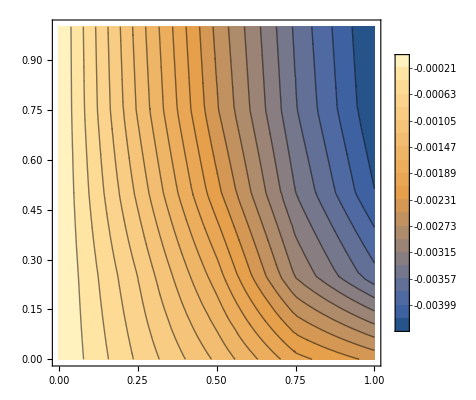

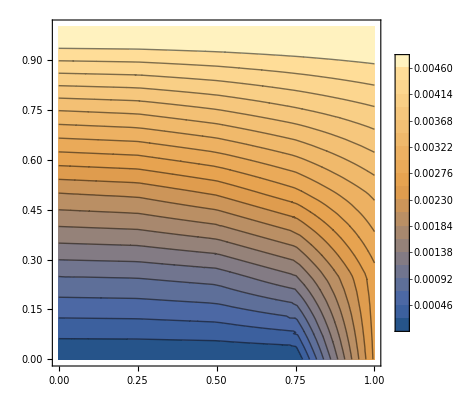

```mathematica
ContourPlot[Ufvec[[1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[Ufvec[[2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 2D

```mathematica
ContourPlot[StressMatf[[1,1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[1,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[2,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[3,3]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Plot Displacement 3D

```mathematica
SliceContourPlot3D[Ufvec[[1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 3D

```mathematica
SliceContourPlot3D[StressMatf[[1,1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```